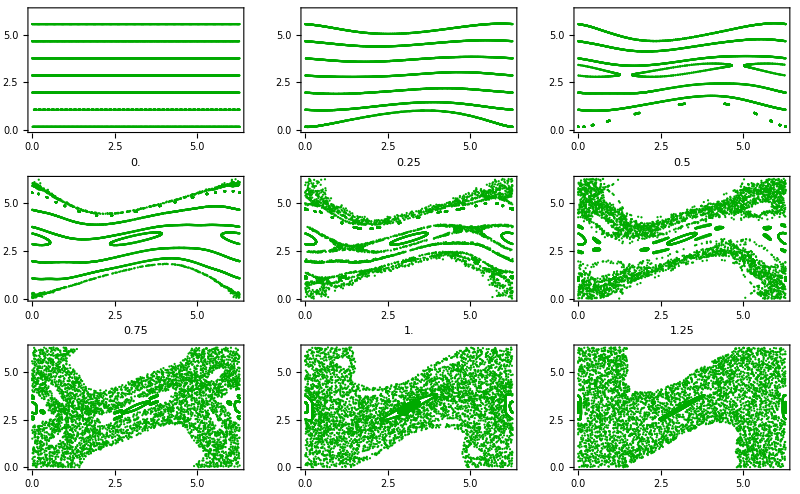

standardmap.jpg

```mathematica
(*
   * Author: Panichi Federico
* Unit Name:chirikov
* Unit Type: program.nb
   * Project: Master Thesis
   * Package: none
   * Language: Mathematica 9.0
   * Description: Plot the phase space of pendulum varing K. Varing this parameter the orbits evolve from ordinary to chaotic. Here is shown different initial conditions (different orbits) in each plot and different value of K between plots.
   * Invocation: none
*)
T[{x_Real,y_Real},g_Real]:=N[Mod[{x+y+g*Sin[x],y+g*Sin[x]},2 Pi]];
Orbit[pO_,n_Integer,g_Real]:=Module[{},S[p_]:=T[p,g];NestList[S,pO,n-1]];
OrbitSet[k_Integer,n_Integer,g_]:=Module[{s={}},
Do[
s=Union[s,Orbit[{0.0,N[2Pi*(0.741629+(i-1)/k)]},n,g]],{i,k}];s];
Pict [k_,m_,g_]:=ListPlot[OrbitSet[k,m,g],PlotRange->{{0,N[2Pi]}, {0,N[2Pi]}},DisplayFunction->Identity,
Frame->True,Axes->False,PlotStyle->{Darker[Green],PointSize[0.004]},
FrameTicks->Automatic,FrameLabel->g];
Film[k_,m_,l_]:=Table[Pict[k,m,0.0+N[(j-1)/4]],{j,l}];

(* k=number of rows, m=number or points, l=number of graphics, N[(j-1)/R R: this change the value of g between plots *)

k=Show[GraphicsGrid[Partition[Film[7,1000,9],3]],
DisplayFunction->$DisplayFunction, Frame->False,
PlotLabel->"The Standard Map family",ImageSize->800]

Export["standardmap.jpg",k]
```

```mathematica
(*
   * Author: Panichi Federico
* Unit Name:chirikov
* Unit Type: program.nb
   * Project: Master Thesis
   * Package: none
   * Language: Mathematica 9.0
   * Description: Using the Chirikov overlap method with two neighboring resonances. Where the resonances overplot the value ok K (y-axis) increase and the motion is chaotic. In x-axis is shown the value of the eccentricity of the resonances. 
   * Invocation: none
*)

j=-1;
a21=3.275794729726671;
a31=2.49999;
a53=3.6991708;
a32=3.9683436;
a43=4.2925064;
alfaF21=0.749964;
alfaF31=0.287852;
alfaF53=2.32892;
alfaF32=1.54553;
alfaF43=2.34472;
mu=10^-3;
tot1=alfaF21*mu;
tot2=alfaF31*mu;
tot3=alfaF53*mu;
tot4=alfaF32*mu;
tot5=alfaF43*mu;

f1[i_]:=a43 (-Sqrt[(16 tot5*i)/3 (1+tot5/(27 i^3))]-(2 tot5)/(9 j*i));
f2[i_]:=a32 (Sqrt[(16 tot4*i)/3 (1+tot4/(27 i^3))]-(2 tot4)/(9 j*i));

s[i_]:=(EuclideanDistance[f1[i],f2[i]]/(a43-a32))^2;

n=ListPlot[Table[{i,s[i]},{i,0.0001,.3,0.0001}],PlotRange->{0.0,2.0},Joined->True,Mesh->None,ClippingStyle->None,AxesLabel->{Style["eccentricità",Italic,15],Style["|(δa_(4 : 3)-δa_(3 : 2))/(a_(4 : 3)-a_(3 : 2))|^2",Italic,15]}];
m=Plot[{1,0.75},{x,0.0,0.3},PlotRange->{0.0,2.0},Filling->{1->{Axis,Directive[Green,Opacity[0.4]]},2->{Axis,Directive[Yellow,Opacity[0.4]]}}];
Show[n,m,ImageSize->500]
```